```mathematica
(*(ccdata[7]/.{x_,y_}/;x>maxyx->{x,0})[[All,2]]*)
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];
fitmin[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,mins[[i]],If[mins[[i]]>0,mins[[i]],1]];;mins[[i+1]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/"<>temp<>"bare.dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/"<>temp<>"bare.dat",res];];

storemin[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/"<>temp<>"min.dat",res];];

storeareamin[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/results/"<>temp<>"min.dat",res];];

import[res_]:=res=Import["spectraldata/Tscan/results/"<>ToString[res]<>".dat"];
```

## Charmonium

### Import Data

```mathematica
Tscanc=Round[1000Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.299,0.003}]]]
```

{150,151,152,153,154,155,156,157,158,159,160,162,165,168,171,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,225,228,231,234,237,240,243,246,249,252,255,258,261,264,267,270,273,276,279,282,285,288,291,294,297}

```mathematica
Do[ccdata[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"spectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdata[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatau[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"uspectra.dat"]/.{a_,b_}:>{a,b a^2};,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatau[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatal[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"lspectra.dat"]/.{a_,b_}:>{a,b a^2};,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatal[n],Joined->True],{n,1,Length[Tscanc],1}]
```

### Fitting

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,Tscanc]];
Quiet[fit[ccdatal,ccmodell,Tscanc]];
Quiet[fit[ccdatau,ccmodelu,Tscanc]];
```

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

### Display Results

```mathematica
import[wrfitcc];
import[wrfitccl];
import[wrfitccu];
import[gfitcc];
import[gfitccl];
import[gfitccu];
import[cfitcc];
import[cfitccl];
import[cfitccu];
import[dfitcc];
import[dfitccl];
import[dfitccu];
import[sfitcc];
import[sfitccl];
import[sfitccu];
import[s2fitcc];
import[s2fitccl];
import[s2fitccu];
import[areafitcc];
import[areafitccl];
import[areafitccu];
```

```mathematica
Do[If[Length[wrfitcc[[-i]]]<2,cc1Tcut=Length[wrfitcc]-i];,{i,Length[wrfitcc]}];
Do[If[Length[wrfitccu[[-i]]]<2,cc1uTcut=Length[wrfitccu]-i];,{i,Length[wrfitccl]}];
Do[If[Length[wrfitccl[[-i]]]<2,cc1lTcut=Length[wrfitccl]-i];,{i,Length[wrfitccu]}];
```

```mathematica
Manipulate[Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitcc],1},{ii,1,Length[wrfitcc[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccl],1},{ii,1,Length[wrfitccl[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitccu],1},{ii,1,Length[wrfitccu[[1]]],1}]
```

```mathematica
cccont={3.6483729114181176,3.628621302148116,3.6101145562570203,3.5927173759648205,3.576314201544601,3.560805658942647,3.546105760749838,3.5321396803039242,3.5188419576608325,3.506155041689381,3.4940281037196854,3.471278788010406,3.440374782969327,3.4126503033211835,3.387518704036325,3.36453530102747,3.34335604976771,3.323710026250687,3.3053805756314762,3.2881920770007516,3.2720004508611926,3.256686218274664,3.2421493399144286,3.228305319625407,3.2150822220303565,3.2026602626391902,3.191119841828597,3.179965550206826,3.1691667884984343,3.158696344598457,3.14852992188661,3.138645746491236,3.129024236912391,3.119647725191289,3.1105002204143117,3.101567206973688,3.0928354734217183,3.0842929633252685,3.0759286436706774,3.067732400490483,3.059694936231515,3.051807686723638,3.044062750599609,3.0364528181839336,3.028971120219355,3.02161137329323,3.014367735723848,3.007234769798351,3.000207401963855,2.993280896328691,2.986450820922096,2.979713026763712,2.9730636213973893,2.9664989504780372,2.9600155779636927,2.9536102704516143,2.9472799787457067};
cccontl={4.0492876135064675,4.009834412583094,3.974039497864153,3.9413567897502153,3.9113475489075267,3.883654735533887,3.8579844752130774,3.8340924192073187,3.8117735287579686,3.790854312097122,3.7711868606206544,3.7351166940341245,3.6877303141478692,3.6466797691454373,3.6105703478706666,3.5784024927140377,3.549438847495361,3.523122118012546,3.499022300568866,3.476801634270089,3.4561906549587658,3.436971422200303,3.4189655145849467,3.402025271340225,3.3860272923671957,3.3712046158602673,3.35764911313572,3.344658646735351,3.3321838597731297,3.320181343734192,3.308612742816771,3.2974440190407677,3.286644843188935,3.2761880876607243,3.2660494017395862,3.2562068536640374,3.246640629751566,3.237332775776361,3.2282669721439645,3.2194283538955735,3.210803339704878,3.202379492680868,3.1941454023424507,3.1860905695796022,3.178205321267219,3.1704807229942715,3.162908507927961,3.155481015957577,3.148191131584507,3.141032240895746,3.1339981798900975,3.127083200868538,3.120281932159078,3.11358934928938,3.1070007448362027,3.100511704313145,3.09411807872051};
cccontu={3.449017567277334,3.4346722714824907,3.421059480842479,3.408110878170136,3.395766798437223,3.383974865458177,3.3726888842881344,3.361867935583532,3.3514756241684855,3.3414794516035653,3.33185029477527,3.313590862018206,3.2883768501192154,3.2653559193134387,3.2441608912584963,3.2245061480814607,3.206165671118878,3.188957906567184,3.1727350828718373,3.157375509172691,3.1427779198792902,3.12885725062126,3.115541436652943,3.102768953206884,3.0904869026356905,3.0788501355947426,3.0679309129979453,3.057321810627566,3.0469996457929214,3.036943676303921,3.027135275843802,3.017557661555675,3.008195662983831,2.9990355256176238,2.9900647430967267,2.98127191310423,2.972646614526729,2.96417929952942,2.955861197488173,2.9476842393676352,2.939640981686896,2.931724545317176,2.9239285633927943,2.916247127756548,2.9086747510522817,2.9012063253675144,2.8938370889814475,2.8865625978790432,2.879378695184011,2.8722814912374797,2.86526733744059,2.858332810398624,2.8514746913335802,2.8446899519349134,2.837975738937902,2.8313293619676103,2.8247482790649};
```

```mathematica
ccbind=cccont-wrfitcc;
ccbindu=cccontu-wrfitccu;
ccbindl=cccontl-wrfitccl;
```

```mathematica
Do[If[(ccbind-gfitcc)[[i,1]]>0,cc1Tmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbind-gfitcc)[[i,2]]>0,cc2Tmelt=i],{i,1,cc1Tcut}];
Do[If[(ccbindl-gfitccl)[[i,1]]>0,cc1lTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindl-gfitccl)[[i,2]]>0,cc2lTmelt=i],{i,1,cc1lTcut}];
Do[If[(ccbindu-gfitccu)[[i,1]]>0,cc1uTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindu-gfitccu)[[i,2]]>0,cc2uTmelt=i,cc2uTmelt=1],{i,1,cc1uTcut}];
```

```mathematica
N[{Tscanc[[cc1lTmelt]],Tscanc[[cc1Tmelt]],Tscanc[[cc1uTmelt]]}/155]
```

{1.81935,1.49032,1.29677}

```mathematica
N[{Tscanc[[cc2lTmelt]],Tscanc[[cc2Tmelt]],Tscanc[[cc2uTmelt]]}/155]
```

{1.08387,0.974194,0.967742}

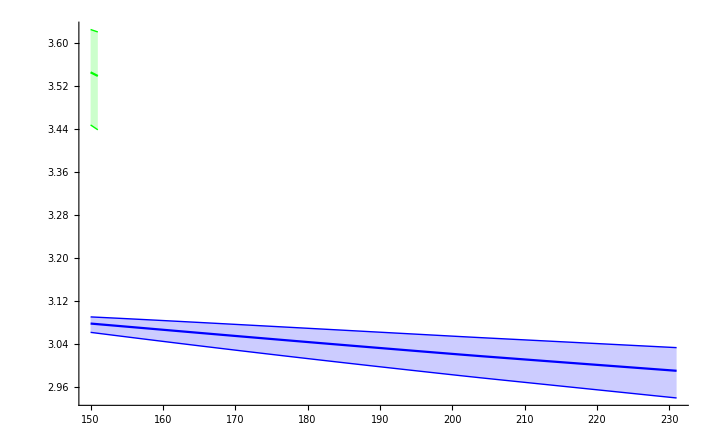

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],wrfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

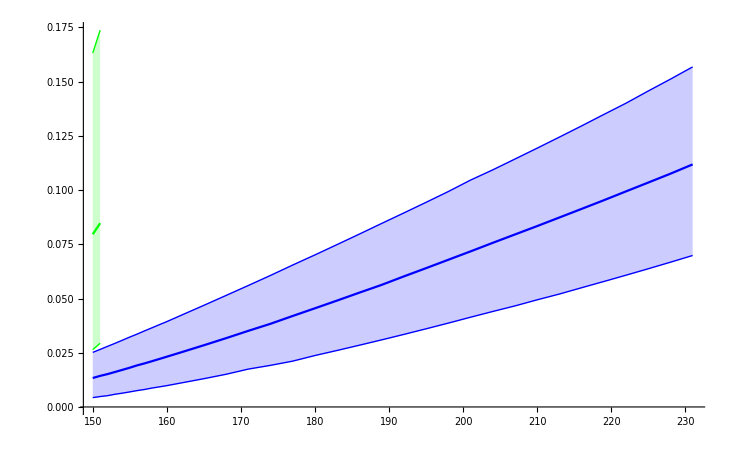

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],gfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],gfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],gfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],gfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],gfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],gfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

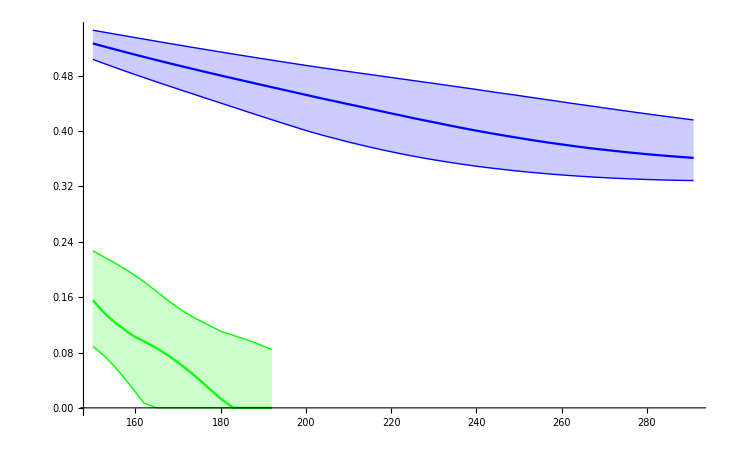

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt+20]],areafitcc[[;;cc1Tmelt+20,1]]}],Transpose[{Tscanc[[;;cc1Tmelt+20]],areafitccl[[;;cc1Tmelt+20,1]]}],Transpose[{Tscanc[[;;cc1Tmelt+20]],areafitccu[[;;cc1Tmelt+20,1]]}],Transpose[{Tscanc[[;;cc2Tmelt+20]],areafitcc[[;;cc2Tmelt+20,2]]}],Transpose[{Tscanc[[;;cc2Tmelt+20]],areafitccl[[;;cc2Tmelt+20,2]]}],Transpose[{Tscanc[[;;cc2Tmelt+20]],areafitccu[[;;cc2Tmelt+20,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

## Charmonium Emission Rates

```mathematica
(*storefine[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/cc/Tcfine/results/"<>temp<>".dat",res];];

storeareafine[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/Tscan/cc/Tcfine/results/"<>temp<>".dat",res];];

importfine[res_]:=res=Import["spectraldata/Tscan/cc/Tcfine/results/"<>ToString[res]<>".dat"];*)
```

```mathematica
Emfactor=2.356305815440891;
nB[w_,T_]:=1/(Exp[w/T]-1);
nBi[w_,T_]:=NIntegrate[p^2 nB[√(w^2+p^2),T] w/(√(w^2+p^2)),{p,0,∞}];
```

```mathematica
areafitcc[[1,1]]
```

0.526696

```mathematica
areafitcc[[1,2]]
```

0.155719

```mathematica
NIntegrate[BWi[w,wrfitcc[[1,1]],gfitcc[[1,1]],cfitcc[[1,1]]],{w,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {3.06375}. NIntegrate obtained 0.526225 and 0.00565422 for the integral and error estimates.

0.526225

```mathematica
NIntegrate[BWi[w,wrfitcc[[1,2]],gfitcc[[1,2]],cfitcc[[1,2]]],{w,0,∞}]
```

0.155163

```mathematica
NIntegrate[BWi[w,wrfitcc[[1,2]],gfitcc[[1,2]],cfitcc[[1,2]]]nB[√(w^2+p^2),Tscanc[[1]]/1000](p^2 w)/(√(w^2+p^2)),{w,0,∞},{p,0,∞},WorkingPrecision->10]/NIntegrate[BWi[w,wrfitcc[[1,1]],gfitcc[[1,1]],cfitcc[[1,1]]]nB[√(w^2+p^2),Tscanc[[1]]/1000](p^2 w)/(√(w^2+p^2)),{w,0,∞},{p,0,∞},WorkingPrecision->10]
```

1.2740504

```mathematica
areafitcc[[1,2]]nB[wrfitcc[[1,2]],Tscanc[[1]]/1000]/(areafitcc[[1,1]]nB[wrfitcc[[1,1]],Tscanc[[1]]/1000])
```

0.0130301

```mathematica
areafitcc[[1,2]]nBi[wrfitcc[[1,2]],Tscanc[[1]]/1000]/(areafitcc[[1,1]]nBi[wrfitcc[[1,1]],Tscanc[[1]]/1000])
```

0.0160773

```mathematica
R0=ConstantArray[0,cc1Tmelt];
Do[R0[[ii]]={Tscanc[[ii]],Emfactor (areafitcc[[ii,2]]nBi[wrfitcc[[ii,2]],Tscanc[[ii]]/1000])/(areafitcc[[ii,1]]nBi[wrfitcc[[ii,1]],Tscanc[[ii]]/1000])},{ii,cc1Tmelt}];
R0l=ConstantArray[0,cc1lTmelt];
Do[R0l[[ii]]={Tscanc[[ii]],Emfactor (areafitccl[[ii,2]]nBi[wrfitccl[[ii,2]],Tscanc[[ii]]/1000])/(areafitccl[[ii,1]]nBi[wrfitccl[[ii,1]],Tscanc[[ii]]/1000])},{ii,cc1lTmelt}];
R0u=ConstantArray[0,cc1uTmelt];
Do[R0u[[ii]]={Tscanc[[ii]],Emfactor (areafitccu[[ii,2]]nBi[wrfitccu[[ii,2]],Tscanc[[ii]]/1000])/(areafitccu[[ii,1]]nBi[wrfitccu[[ii,1]],Tscanc[[ii]]/1000])},{ii,cc1uTmelt}];
```

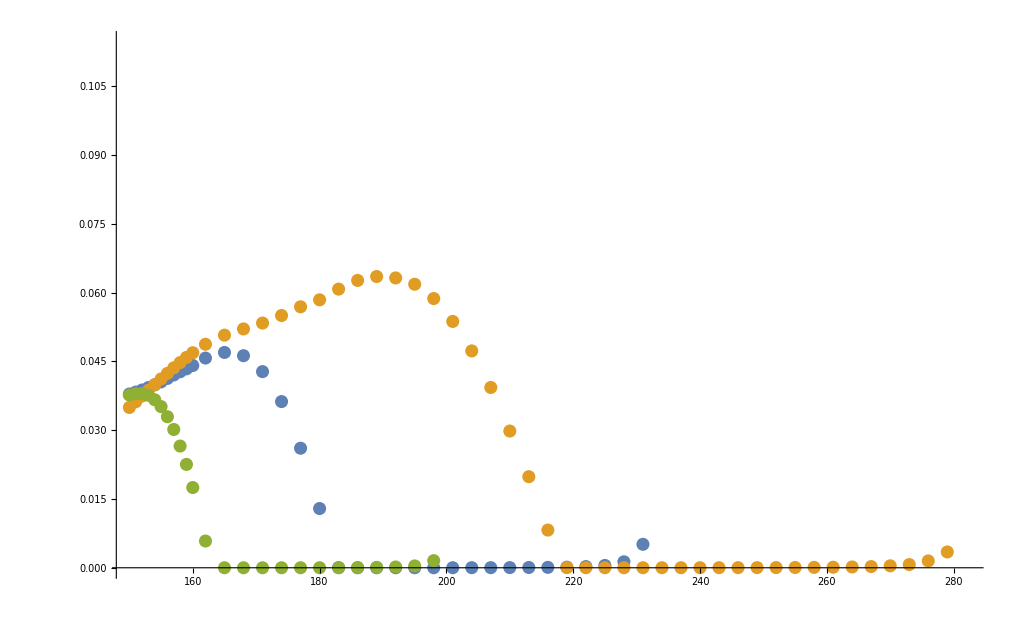

```mathematica
ListPlot[{R0,R0l,R0u}]
```

```mathematica
R0[[6]]
```

{155,0.0332438}

```mathematica
R0u[[6]]
```

{155,0.0298952}

```mathematica
R0l[[6]]
```

{155,0.0327234}

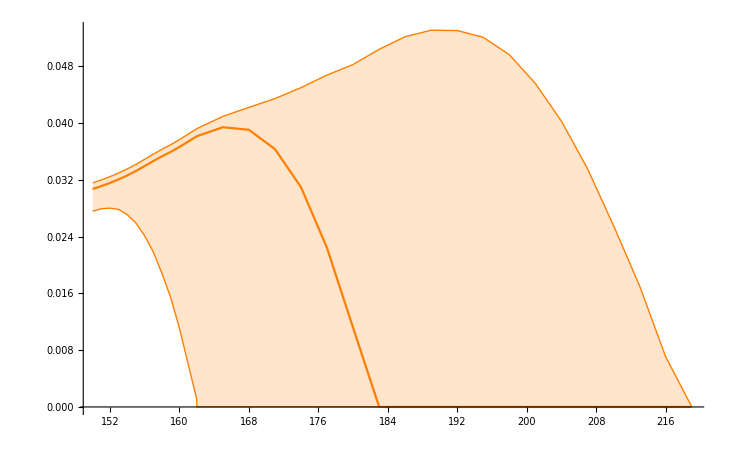

```mathematica
ListPlot[{Append[Append[R0[[;;-17]],{183.1,0}],{219,0}],Join[R0[[;;12]]/.{x_,y_}:>{x,y R0u[[1,2]]/R0[[1,2]]},R0l[[13;;31]]],Append[Append[R0u[[;;-14]]-(R0u[[1,2]]-R0l[[1,2]]),{162,0.}],{183,0.}]},PlotRange->All,Joined->True,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2],PlotStyle->{Orange,{Orange,Thin},{Orange,Thin}}]
```

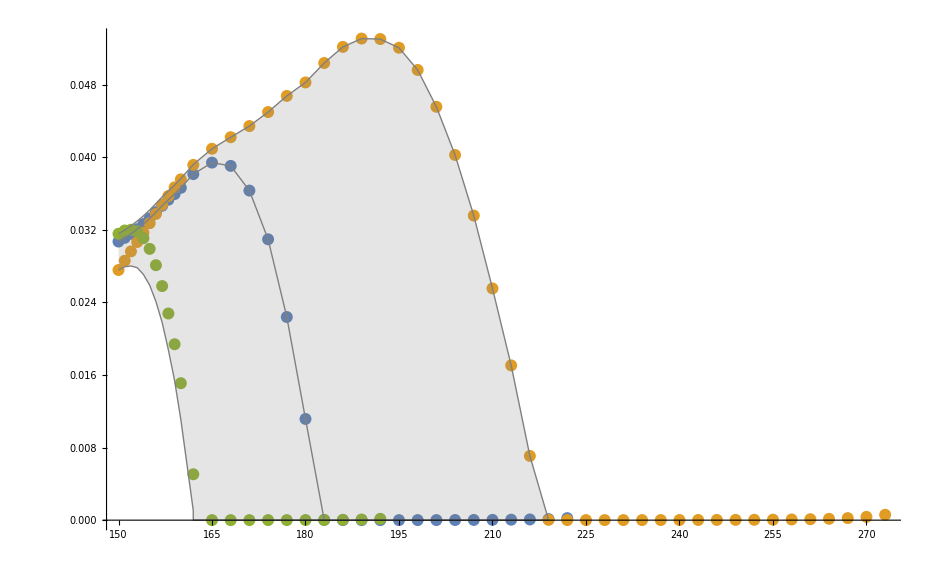

```mathematica
Show[{ListPlot[{R0[[;;-4]],R0l[[;;-4]],R0u[[;;-4]]}],ListPlot[{Append[Append[R0[[;;-17]],{183.1,0}],{219,0}],Join[R0[[;;12]]/.{x_,y_}:>{x,y R0u[[1,2]]/R0[[1,2]]},R0l[[13;;31]]],Append[Append[R0u[[;;-14]]-(R0u[[1,2]]-R0l[[1,2]]),{162,0.}],{183,0.}]},PlotRange->All,Joined->True,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2],PlotStyle->{{Gray,Thin},{Gray,Thin},{Gray,Thin}}]}]
```

## Bottomonium

```mathematica
Tscanb=IntegerPart[1000 Table[i,{i,0.15,0.6,0.005}]]
```

{150,155,160,164,169,175,180,185,190,195,200,205,210,215,220,224,229,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,329,334,339,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,439,444,449,454,459,464,470,475,480,485,490,495,500,505,510,515,520,525,530,535,540,545,550,555,560,565,570,575,580,585,590,595,600}

```mathematica
Do[bbdata[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"spectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdata[n],Joined->True],{n,1,Length[Tscanb],1}]
```

```mathematica
Do[bbdatal[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"lspectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdatal[n],Joined->True],{n,1,Length[Tscanb],1}]
```

```mathematica
Do[bbdatau[n]=Import["spectraldata/Tscan/bb/swbbT"<>ToString[Tscanb[[n]]]<>"uspectra.dat"];,{n,Length[Tscanb]}];
Manipulate[ListPlot[bbdatau[n],Joined->True],{n,1,Length[Tscanb],1}]
```

### Fitting

```mathematica
Clear[bbmodel,bbmodelu,bbmodell]
fitnew[bbdata,bbmodel,Tscanb];
fitnew[bbdatau,bbmodelu,Tscanb];
fitnew[bbdatal,bbmodell,Tscanb];
```

### Store Results

```mathematica
Do[If[Length[bbmodel[[i]]]>4,bbmodel[[i]]=bbmodel[[i,;;4]]];If[Length[bbmodelu[[i]]]>4,bbmodelu[[i]]=bbmodelu[[i,;;4]]];If[Length[bbmodell[[i]]]>4,bbmodell[[i]]=bbmodell[[i,;;4]]];,{i,Length[bbmodel]}];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

### Display Results

```mathematica
import[wrfitbb];
import[wrfitbbl];
import[wrfitbbu];
import[gfitbb];
import[gfitbbl];
import[gfitbbu];
import[cfitbb];
import[cfitbbl];
import[cfitbbu];
import[dfitbb];
import[dfitbbl];
import[dfitbbu];
import[sfitbb];
import[sfitbbl];
import[sfitbbu];
import[s2fitbb];
import[s2fitbbl];
import[s2fitbbu];
import[areafitbb];
import[areafitbbl];
import[areafitbbu];
```

```mathematica
Do[If[Length[wrfitbb[[-i]]]<2,bb1Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<2,bb1uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<2,bb1lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<3,bb2Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<3,bb2uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<3,bb2lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<4,bb3Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];Do[If[Length[wrfitbbu[[-i]]]<4,bb3uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];Do[If[Length[wrfitbbl[[-i]]]<4,bb3lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
```

```mathematica
Manipulate[Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[wrfitbb],1},{ii,1,Length[wrfitbb[[1]]],1}]
```

ListPlot::lpn: bbdata[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitbb⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitbb⟦1,1⟧ in {x,0.7 wrfitbb⟦1,1⟧,1.3 wrfitbb⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[bbdata[1],Joined→True],Plot[BW[x,wrfitbb⟦FE`i$$232,FE`ii$$232⟧,gfitbb⟦FE`i$$232,FE`ii$$232⟧,dfitbb⟦FE`i$$232,FE`ii$$232⟧,cfitbb⟦FE`i$$232,FE`ii$$232⟧,sfitbb⟦FE`i$$232,FE`ii$$232⟧,s2fitbb⟦FE`i$$232,FE`ii$$232⟧],{x,0.7 wrfitbb⟦FE`i$$232,FE`ii$$232⟧,1.3 wrfitbb⟦FE`i$$232,FE`ii$$232⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitbb⟦FE`i$$232,FE`ii$$232⟧,gfitbb⟦FE`i$$232,FE`ii$$232⟧,cfitbb⟦FE`i$$232,FE`ii$$232⟧],{x,0.7 wrfitbb⟦FE`i$$232,FE`ii$$232⟧,1.3 wrfitbb⟦FE`i$$232,FE`ii$$232⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitbb⟦1,1⟧ in {x,0.7 wrfitbb⟦1,1⟧,1.3 wrfitbb⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[bbdata[1],Joined→True],Plot[BW[x,wrfitbb⟦FE`i$$232,FE`ii$$232⟧,gfitbb⟦FE`i$$232,FE`ii$$232⟧,dfitbb⟦FE`i$$232,FE`ii$$232⟧,cfitbb⟦FE`i$$232,FE`ii$$232⟧,sfitbb⟦FE`i$$232,FE`ii$$232⟧,s2fitbb⟦FE`i$$232,FE`ii$$232⟧],{x,0.7 wrfitbb⟦FE`i$$232,FE`ii$$232⟧,1.3 wrfitbb⟦FE`i$$232,FE`ii$$232⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitbb⟦FE`i$$232,FE`ii$$232⟧,gfitbb⟦FE`i$$232,FE`ii$$232⟧,cfitbb⟦FE`i$$232,FE`ii$$232⟧],{x,0.7 wrfitbb⟦FE`i$$232,FE`ii$$232⟧,1.3 wrfitbb⟦FE`i$$232,FE`ii$$232⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

ListPlot::lpn: bbdata[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitbb⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitbb⟦1,1⟧ in {x,0.7 wrfitbb⟦1,1⟧,1.3 wrfitbb⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[bbdata[1],Joined→True],Plot[BW[x,wrfitbb⟦FE`i$$121,FE`ii$$121⟧,gfitbb⟦FE`i$$121,FE`ii$$121⟧,dfitbb⟦FE`i$$121,FE`ii$$121⟧,cfitbb⟦FE`i$$121,FE`ii$$121⟧,sfitbb⟦FE`i$$121,FE`ii$$121⟧,s2fitbb⟦FE`i$$121,FE`ii$$121⟧],{x,0.7 wrfitbb⟦FE`i$$121,FE`ii$$121⟧,1.3 wrfitbb⟦FE`i$$121,FE`ii$$121⟧},PlotStyle→{«1»},PlotRange→All],Plot[BWi[x,wrfitbb⟦FE`i$$121,FE`ii$$121⟧,gfitbb⟦FE`i$$121,FE`ii$$121⟧,cfitbb⟦FE`i$$121,FE`ii$$121⟧],{x,0.7 wrfitbb⟦FE`i$$121,FE`ii$$121⟧,1.3 wrfitbb⟦FE`i$$121,FE`ii$$121⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitbb⟦1,1⟧ in {x,0.7 wrfitbb⟦1,1⟧,1.3 wrfitbb⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[bbdata[1],Joined→True],Plot[BW[x,wrfitbb⟦FE`i$$121,FE`ii$$121⟧,gfitbb⟦FE`i$$121,FE`ii$$121⟧,dfitbb⟦FE`i$$121,FE`ii$$121⟧,cfitbb⟦FE`i$$121,FE`ii$$121⟧,sfitbb⟦FE`i$$121,FE`ii$$121⟧,s2fitbb⟦FE`i$$121,FE`ii$$121⟧],{x,0.7 wrfitbb⟦FE`i$$121,FE`ii$$121⟧,1.3 wrfitbb⟦FE`i$$121,FE`ii$$121⟧},PlotStyle→{«1»},PlotRange→All],Plot[BWi[x,wrfitbb⟦FE`i$$121,FE`ii$$121⟧,gfitbb⟦FE`i$$121,FE`ii$$121⟧,cfitbb⟦FE`i$$121,FE`ii$$121⟧],{x,0.7 wrfitbb⟦FE`i$$121,FE`ii$$121⟧,1.3 wrfitbb⟦FE`i$$121,FE`ii$$121⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

ListPlot::lpn: bbdata[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitbb⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitbb⟦1,1⟧ in {x,0.7 wrfitbb⟦1,1⟧,1.3 wrfitbb⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[bbdata[1],Joined→True],Plot[BW[x,wrfitbb⟦FE`i$$59,FE`ii$$59⟧,gfitbb⟦FE`i$$59,FE`ii$$59⟧,dfitbb⟦FE`i$$59,FE`ii$$59⟧,cfitbb⟦FE`i$$59,FE`ii$$59⟧,sfitbb⟦FE`i$$59,FE`ii$$59⟧,s2fitbb⟦FE`i$$59,FE`ii$$59⟧],{x,0.7 wrfitbb⟦FE`i$$59,FE`ii$$59⟧,1.3 wrfitbb⟦FE`i$$59,FE`ii$$59⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitbb⟦FE`i$$59,FE`ii$$59⟧,gfitbb⟦FE`i$$59,FE`ii$$59⟧,cfitbb⟦FE`i$$59,FE`ii$$59⟧],{x,0.7 wrfitbb⟦FE`i$$59,FE`ii$$59⟧,1.3 wrfitbb⟦FE`i$$59,FE`ii$$59⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitbb⟦1,1⟧ in {x,0.7 wrfitbb⟦1,1⟧,1.3 wrfitbb⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[bbdata[1],Joined→True],Plot[BW[x,wrfitbb⟦FE`i$$59,FE`ii$$59⟧,gfitbb⟦FE`i$$59,FE`ii$$59⟧,dfitbb⟦FE`i$$59,FE`ii$$59⟧,cfitbb⟦FE`i$$59,FE`ii$$59⟧,sfitbb⟦FE`i$$59,FE`ii$$59⟧,s2fitbb⟦FE`i$$59,FE`ii$$59⟧],{x,0.7 wrfitbb⟦FE`i$$59,FE`ii$$59⟧,1.3 wrfitbb⟦FE`i$$59,FE`ii$$59⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitbb⟦FE`i$$59,FE`ii$$59⟧,gfitbb⟦FE`i$$59,FE`ii$$59⟧,cfitbb⟦FE`i$$59,FE`ii$$59⟧],{x,0.7 wrfitbb⟦FE`i$$59,FE`ii$$59⟧,1.3 wrfitbb⟦FE`i$$59,FE`ii$$59⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

ListPlot::lpn: bbdata[1.] is not a list of numbers or pairs of numbers.

Part::partd: Part specification wrfitbb⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0.7 wrfitbb⟦1,1⟧ in {x,0.7 wrfitbb⟦1,1⟧,1.3 wrfitbb⟦1,1⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[bbdata[1],Joined→True],Plot[BW[x,wrfitbb⟦FE`i$$29,FE`ii$$29⟧,gfitbb⟦FE`i$$29,FE`ii$$29⟧,dfitbb⟦FE`i$$29,FE`ii$$29⟧,cfitbb⟦FE`i$$29,FE`ii$$29⟧,sfitbb⟦FE`i$$29,FE`ii$$29⟧,s2fitbb⟦FE`i$$29,FE`ii$$29⟧],{x,0.7 wrfitbb⟦FE`i$$29,FE`ii$$29⟧,1.3 wrfitbb⟦FE`i$$29,FE`ii$$29⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitbb⟦FE`i$$29,FE`ii$$29⟧,gfitbb⟦FE`i$$29,FE`ii$$29⟧,cfitbb⟦FE`i$$29,FE`ii$$29⟧],{x,0.7 wrfitbb⟦FE`i$$29,FE`ii$$29⟧,1.3 wrfitbb⟦FE`i$$29,FE`ii$$29⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

Plot::plln: Limiting value 0.7 wrfitbb⟦1,1⟧ in {x,0.7 wrfitbb⟦1,1⟧,1.3 wrfitbb⟦1,1⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[bbdata[1],Joined→True],Plot[BW[x,wrfitbb⟦FE`i$$29,FE`ii$$29⟧,gfitbb⟦FE`i$$29,FE`ii$$29⟧,dfitbb⟦FE`i$$29,FE`ii$$29⟧,cfitbb⟦FE`i$$29,FE`ii$$29⟧,sfitbb⟦FE`i$$29,FE`ii$$29⟧,s2fitbb⟦FE`i$$29,FE`ii$$29⟧],{x,0.7 wrfitbb⟦FE`i$$29,FE`ii$$29⟧,1.3 wrfitbb⟦FE`i$$29,FE`ii$$29⟧},PlotStyle→{Red,Dashed},PlotRange→All],Plot[BWi[x,wrfitbb⟦FE`i$$29,FE`ii$$29⟧,gfitbb⟦FE`i$$29,FE`ii$$29⟧,cfitbb⟦FE`i$$29,FE`ii$$29⟧],{x,0.7 wrfitbb⟦FE`i$$29,FE`ii$$29⟧,1.3 wrfitbb⟦FE`i$$29,FE`ii$$29⟧},PlotStyle→{Green,Dashed},PlotRange→All]}].

```mathematica
bbcont={10.47459661653534,10.386991291819312,10.320189935556595,10.266520483724824,10.221771783701307,10.183415247448838,10.14982884042086,10.119917801704643,10.092912804537864,10.068255145767312,10.045527844650223,10.024869142170065,10.00606442137611,9.988248930352256,9.971300912748175,9.955119189686751,9.939618860084348,9.924728047184722,9.91038541425775,9.896538234463003,9.883140878360269,9.870153615237932,9.857541654132588,9.84527436973816,9.833324672428462,9.821668491664653,9.810284349405235,9.799153005449387,9.788257160460661,9.777581207953114,9.76711102016143,9.756833770672042,9.746737782242517,9.736812392434949,9.727047840979282,9.717435173901784,9.7079661552598,9.698633193697498,9.68942927922979,9.680347923072885,9.67138310961781,9.662529251650565,9.653781149410847,9.645133958371117,9.636583155264336,9.628124512339577,9.61975407153492,9.611468121959486,9.603263180915544,9.595135974071855,9.587083421208572,9.579102619219741,9.571190830899964,9.563345470697755,9.555564095574915,9.547844393123798,9.540184174031799,9.53258136207098,9.525033987912632,9.517540180573716,9.510098162358636,9.502706241507756,9.495362807980896,9.488066327240787,9.48081533651431,9.473608439770503,9.466444304106242,9.459321655963414,9.452239277450436,9.445196003567682,9.438190718761756,9.431222354618207,9.424289886819881,9.41739233320969,9.41052875109574,9.403698235563585,9.396899917176915,9.390132960386843,9.38339656168247,9.376689947990425,9.370012375266969,9.36336312688355,9.35674151254152,9.350146866770242,9.343578547940272,9.33703593705241,9.330518436688472,9.324025470075904,9.317556480121242,9.311110928532827,9.30468829499006};
```

```mathematica
bbcontl={10.874752316247209,10.709348069405426,10.596996983853511,10.513609526664556,10.448050062654799,10.394377961943272,10.349100389805146,10.310013199330372,10.275648390839436,10.244985723301182,10.217291240093466,10.192656427134342,10.17070083709334,10.150179417217462,10.130898694948609,10.112700563371412,10.09545434620659,10.079050929257686,10.06339836626425,10.048418528941538,10.034044525430874,10.020218685932695,10.00689097404341,9.994017721286706,9.98156060985683,9.969485847976985,9.957763496194124,9.946366912891172,9.935272294413215,9.924458294065756,9.913905696702223,9.90359715051309,9.893516938772313,9.883650780248214,9.873985662596134,9.864509701325682,9.855212011249385,9.846082599813219,9.837112275769512,9.828292562976062,9.81961563171522,9.811074235092388,9.802661651139303,9.794371637465265,9.786198383598345,9.778136475103457,9.770180857650889,9.762326805812604,9.754569896973951,9.746905983922625,9.739331175545635,9.731841813362315,9.724434456566103,9.717105862390124,9.709852974075199,9.702672904521538,9.695562926502934,9.68852045889942,9.68154305879914,9.674628409712207,9.66777431524974,9.660978688961679,9.654239549172559,9.647555010387574,9.640923278713544,9.634342644998762,9.62781148025183,9.621328230674246,9.614891412742095,9.608499609808543,9.602151467377281,9.5958456903678,9.589581038903399,9.583356326100771,9.577170414297424,9.57102221316282,9.56491067649701,9.558834800375598,9.552793620679699,9.546786211051996,9.54081168120238,9.534869174654393,9.528957867624023,9.523076966842094,9.517225708521403,9.51140335671006,9.50560920195353,9.499842560187231,9.494102771471903,9.48838919889178,9.482701227510523};
```

```mathematica
bbcontu={10.27542190323936,10.210306841307867,10.15813391734028,10.11462599593822,10.077265424837341,10.044459777661434,10.015145362901704,9.98858052848785,9.964229937359468,9.941695968597415,9.9206761123795,9.901314731636493,9.883457006803193,9.866397905341865,9.850044414651597,9.834318525972737,9.819154228885557,9.80449520814989,9.790293066036469,9.776505926422514,9.763097330640862,9.750035354706515,9.737291897306735,9.724842100702306,9.712663876105138,9.700737511905654,9.68904534815287,9.677571504347467,9.666301650244467,9.65522281351977,9.644323212761897,9.633592118643751,9.623019734229503,9.612597088822872,9.602315948680184,9.592168740676637,9.58214848184051,9.57224872049114,9.562463485331138,9.55278723703638,9.543214829303091,9.53374147251674,9.524362700565154,9.515074344335435,9.505872504173217,9.49675352858603,9.487713993107569,9.478750681784883,9.46986057136048,9.461040815122214,9.45228873076509,9.443601786640313,9.434977592036402,9.426413885695805,9.417908527788732,9.409459490359788,9.401064850625268,9.392722782960972,9.38443155330194,9.376189512350782,9.367995090888918,9.35984679399565,9.351743197060335,9.343682940911478,9.335664728303266,9.327687319912036,9.31974953110982,9.311850228764314,9.303988328216592,9.29616279070657,9.288372620665468,9.28061686349764,9.272894603234423,9.265204960598545,9.25754709096879,9.249920182665566,9.242323455202108,9.234756157743245,9.22721756760527,9.219706988873012,9.212223751090171,9.204767208043139,9.19733673658531,9.189931735582011,9.182551624856343,9.17519584424124,9.167863852678373,9.160555127338563,9.153269162822552,9.146005470394678,9.138763577258592};
```

```mathematica
bbbind=bbcont-wrfitbb;
bbbindu=bbcontu-wrfitbbu;
bbbindl=bbcontl-wrfitbbl;
```

```mathematica
Do[If[(bbbind-gfitbb)[[i,1]]>0,bb1Tmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbind-gfitbb)[[i,2]]>0,bb2Tmelt=i],{i,1,bb1Tcut}];
Do[If[(bbbind-gfitbb)[[i,3]]>0,bb3Tmelt=i],{i,1,bb2Tcut}];
Do[If[(bbbind-gfitbb)[[i,4]]>0,bb4Tmelt=i,bb4Tmelt=1],{i,1,bb3Tcut}];
```

```mathematica
Do[If[(bbbindu-gfitbbu)[[i,1]]>0,bb1uTmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbindu-gfitbbu)[[i,2]]>0,bb2uTmelt=i],{i,1,bb1uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,3]]>0,bb3uTmelt=i,bb3uTmelt=1],{i,1,bb2uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,4]]>0,bb4uTmelt=i,bb4uTmelt=1],{i,1,bb3uTcut}];
```

```mathematica
Do[If[(bbbindl-gfitbbl)[[i,1]]>0,bb1lTmelt=i+1],{i,1,Length[bbbind]}];
Do[If[(bbbindl-gfitbbl)[[i,2]]>0,bb2lTmelt=i+1],{i,1,bb1lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,3]]>0,bb3lTmelt=i+1],{i,1,bb2lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,4]]>0,bb4lTmelt=i+1],{i,1,bb3lTcut}];
```

```mathematica
N[{Tscanb[[bb1lTmelt]],Tscanb[[bb1Tmelt]],Tscanb[[bb1uTmelt]]}/155]
```

{3.70968,3.03226,2.58065}

```mathematica
N[{Tscanb[[bb2lTmelt]],Tscanb[[bb2Tmelt]],Tscanb[[bb2uTmelt]]}/155]
```

{1.6129,1.32258,1.16129}

```mathematica
N[{Tscanb[[bb3lTmelt]],Tscanb[[bb3Tmelt]],Tscanb[[bb3uTmelt]]}/155]
```

{1.19355,1.03226,0.967742}

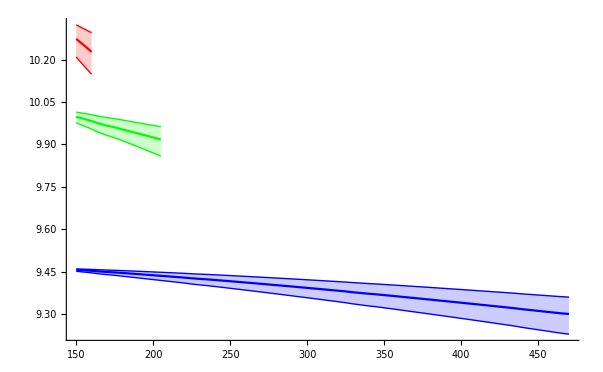

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],wrfitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],wrfitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],wrfitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

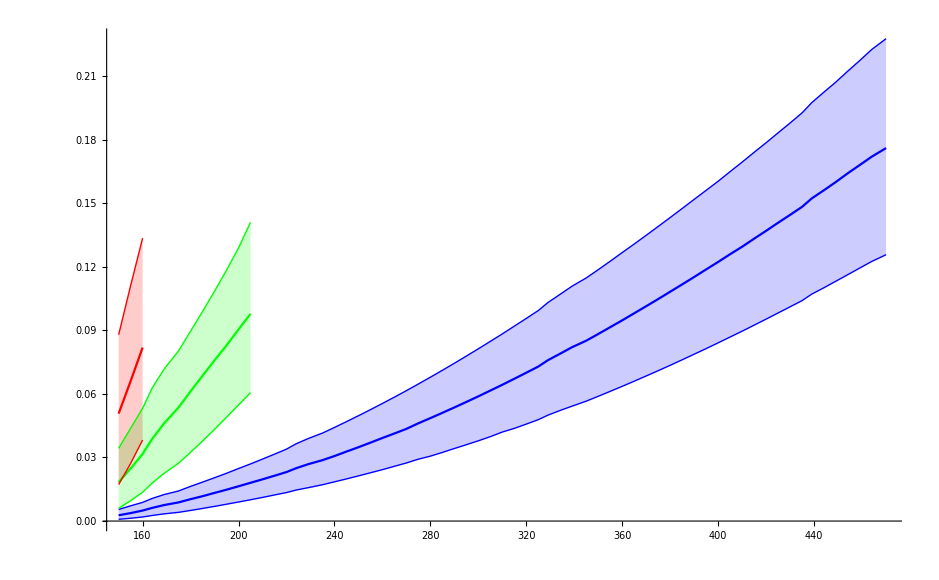

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],gfitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],gfitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],gfitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],gfitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],gfitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],gfitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],gfitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],gfitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],gfitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

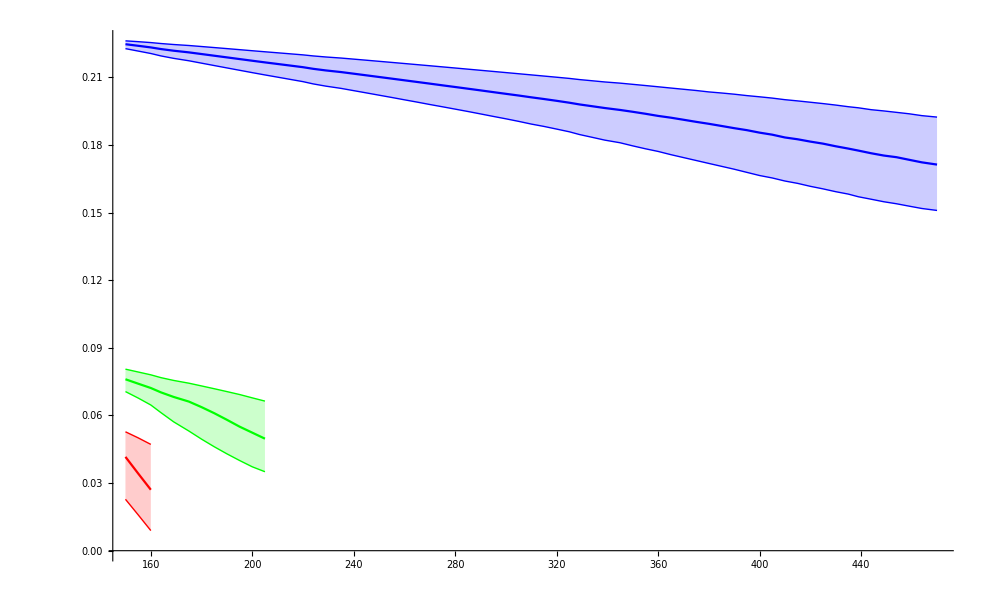

```mathematica
ListPlot[{Transpose[{Tscanb[[;;bb1Tmelt]],areafitbb[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],areafitbbl[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb1Tmelt]],areafitbbu[[;;bb1Tmelt,1]]}],Transpose[{Tscanb[[;;bb2Tmelt]],areafitbb[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],areafitbbl[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb2Tmelt]],areafitbbu[[;;bb2Tmelt,2]]}],Transpose[{Tscanb[[;;bb3Tmelt]],areafitbb[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],areafitbbl[[;;bb3Tmelt,3]]}],Transpose[{Tscanb[[;;bb3Tmelt]],areafitbbu[[;;bb3Tmelt,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```